```mathematica
Exit[]
```

# Value Function

The value function is the value of the solution of the maximization or minimization problem. It is a function of the parameters (constants) of the maximization problem.

In the example below:

The optimization problem is to find the quantity q that maximizes profits given the price p.

The solution of the problem is q(p).

Plugging the solution q(p) into the profits, p*q(p)-c(q(p)) we get the value function

The value function is a function of the price V(p)=p*q(p)-c(q(p)) .

```mathematica
c[q_]:=4*q^2+q+10 (* total cost *)
```

```mathematica
c[10]
```

420

```mathematica
profit[p_,q_]:=p*q-c[q]
```

```mathematica
constraint=-q<=0
```

-q≤0

```mathematica
L[p_,q_,λ_]:=profit[p,q]-λ*(-q-0)
```

```mathematica
D[L[p,q,λ],λ]==0
```

q==0

Case 1: λ>0 then q=0

```mathematica
eqs=Thread[Grad[L[p,q,λ],{q,λ}]==0]
```

{-1+p-8 q+λ==0,q==0}

```mathematica
sol1=Solve[eqs,{q,λ}][[1]]
```

{q→0,λ→1-p}

This case is consistent if and only if 0 ≤ p < 1.

Case 2: λ=0

```mathematica
sol2=Solve[{D[L[p,q,λ],q]==0,λ==0},{q,λ}][[1]]
```

{q→1/8 (-1+p),λ→0}

This case is consistent if and only if 1 ≤ p .

## Value function when 1 ≤ p

```mathematica
V2[p_]:=profit[p,q]/.sol2
```

```mathematica
Simplify[V2[p]]
```

1/16 (-159-2 p+p^2)

## Value function when 0 ≤ p <1

```mathematica
V1[p_]:=profit[p,q]/.sol1
```

```mathematica
V1[p]
```

-10

```mathematica
-c[0]
```

-10

```mathematica
qs[p_]:=Piecewise[{{0,0≤p<1},{(p-1)/8,1<p}}]
```

```mathematica
V[p_]:=Piecewise[{{V1[p],0≤p<1},{V2[p],1<p}}]
```

```mathematica
Plot[V[p],{p,0,20}]
```

Below we plot the value function.

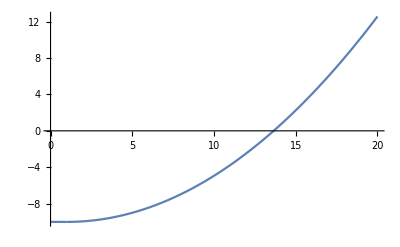

### The Envelope Theorem: An example

What is the marginal impact of a price change on the profits? If we know the value function, the answer is quite simple: It is the derivative of the value function wrt. the price.

```mathematica
D[V[p],p]
```

Piecewise[{{0, p<0||0<p<1}, {1/16 (-2+2 p), p>1}, {Indeterminate, True}}]

But what if we do not have the value function? In principle, seems we have to account for three changes:

A change in the price changes the firm’s revenue p×q^s directly thru the price p.

A change in the price changes the firm’s revenue p×q^s indirectly thru the quantity supply q^s(p).

A change in the price changes the firm’s costs c(q^s) indirectly thru the quantity supply  q^s(p).

However, the envelope theorem states that we only need to look at the DIRECT impact (1) we can ignore the indirect effects in (2) and (3).

Consider this numerical example. When p=10  the firm will supplies 1.125 units. Let’s take a look at the firm profits when the price changes BUT the quantity stays put at qc=1.125

```mathematica
qc=qs[10.]
profit[p,qc]
```

1.125

-16.1875+1.125 p

Below we plot the profit function of the firm (max profits for any price level p) and the profit level of the firm when the quantity is set to qc=1.125

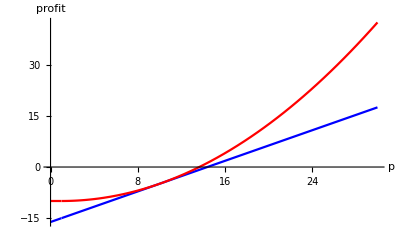

```mathematica
Plot[{profit[p,qc],V[p]},{p,0,30},PlotStyle->{Blue,Red},AxesLabel->{"p","profit"}]
```

Notice that the profit function is always above the profits of producing 1.125 but when p=10, the profit function coincides with it. So the two curves are tangent at the point. If they are tangent, their slopes (derivatives) must be the same.

```mathematica
D[profit[p,qc],p]
```

1.125

```mathematica
D[V[p],p]/.p->10.
```

1.125

Thus, in general the marginal profit of a price increase is simply the quantity being supplied. D[V[p],p]==qs[p]